# Deep Quantum Neural Networks

## Definitions of Functions

General Functions

```mathematica
Clear["Global`*"];
(*Define qubit states*)
qubit0={1,0};qubit1={0,1};

(*The Partial Trace*)
PartialTrace[densityMatrix_,traceList_,quditDim_:2]:=Module[{t=Flatten@{traceList},qubitNum=Log[quditDim,Length@densityMatrix]},ArrayReshape[TensorContract[ArrayReshape[densityMatrix,Table[quditDim,2qubitNum]],Table[{i,i+qubitNum},{i,t}]],{quditDim^(qubitNum-Length@t),quditDim^(qubitNum-Length@t)}]]

(*The SWAP gate*)
SWAP[qubitNum_,qubit1_,qubit2_]:=If[qubit1==qubit2,IdentityMatrix@(2^qubitNum),Normal@SparseArray[1+FromDigits[#,2]&/@{#,Permute[#,Cycles[{{qubit1,qubit2}}]]}->1&/@Tuples[{0,1},qubitNum]]]

(*Convert a vector state to a density matrix*)
DM[state_]:=Outer[Times,state,state*]
```

Training Data & Initial Unitaries

```mathematica
(*Generate a random unitary*)
RU[dim_]:=Orthogonalize@Table[RandomVariate@NormalDistribution[0,1]+ⅈ*RandomVariate@NormalDistribution[0,1],dim,dim]

(*Generate a random state*)
RandomState[dim_]:=Normalize@Table[RandomVariate@NormalDistribution[0,1]+ⅈ*RandomVariate@NormalDistribution[0,1],dim]

(*Generate a set of random training data*)
TrainingData[num_,uni_]:=Module[{tempstate,dim=Length@uni},Table[{tempstate=RandomState@dim,uni.tempstate},num]]

(*Combine the input state with the new added qubits at the lth layer*)
LayerState[inputState_,qubitNum_]:=KroneckerProduct@@Join[{inputState},Table[DM@qubit0,qubitNum]]

(*Convert the unitary of the jth qubit to a full unitary in the lth layer*)
LayerUnitary[architecture_,l_,j_,uni_]:=Module[{swap=SWAP[architecture⟦l-1⟧+architecture⟦l⟧,architecture⟦l-1⟧+1,architecture⟦l-1⟧+j]},
swap.KroneckerProduct[uni,IdentityMatrix@(2^(architecture⟦l⟧-1))].swap]

(*Random initial unitaries*)
InitialUnitaries[architecture_]:=Table[If[l==1,{},LayerUnitary[architecture,l,j,RU@(2^(architecture⟦l-1⟧+1))]],{l,Length@architecture},{j,architecture⟦l⟧}]
```

Quantum Channels

```mathematica
(*Apply the unitaries of the lth layer forward*)
LayerFeedforward[architecture_,currentUnitaries_,l_,j_,inputState_]:=Module[{
layerState=LayerState[inputState,architecture⟦l⟧],
midUnitary=Dot@@Reverse@currentUnitaries⟦l,;;j⟧},
midUnitary.layerState.midUnitary†]

(*Generate a channel ℰ for the lth layer in the network*)
LayerChannel[architecture_,currentUnitaries_,l_,inputState_]:=PartialTrace[LayerFeedforward[architecture,currentUnitaries,l,architecture⟦l⟧,inputState],Range@architecture⟦l-1⟧]

(*Apply the unitaries of the lth layer backward*)
LayerBackPropagate[architecture_,currentUnitaries_,l_,j_,outputState_]:=Module[{
layerState=KroneckerProduct[IdentityMatrix@(2^architecture⟦l-1⟧),outputState],
layerUnitary=If[j<architecture⟦l⟧,Dot@@Reverse@currentUnitaries⟦l,j+1;;⟧,IdentityMatrix@(2^(architecture⟦l-1⟧+architecture⟦l⟧))]},
layerUnitary†.layerState.layerUnitary]

(*Generate an adjoint channel ℱ for the lth layer in the network*)
AdjointLayerChannel[architecture_,currentUnitaries_,l_,outputState_]:=
PartialTrace[LayerState[IdentityMatrix@(2^architecture⟦l-1⟧),architecture⟦l⟧].LayerBackPropagate[architecture,currentUnitaries,l,0,outputState],architecture⟦l-1⟧+Range@architecture⟦l⟧]

(*The whole feedforward process*)
Feedforward[architecture_,trainingData_,currentUnitaries_]:=Table[FoldList[LayerChannel[architecture,currentUnitaries,#2,#1]&,DM@trainingData⟦n,1⟧,Range[2,Length@architecture]],{n,Length@trainingData}]

(*The back propagation to lth layer, i.e., the so-called σx in the paper*)
BackPropagate[architecture_,currentUnitaries_,l_,outputState_]:=Fold[AdjointLayerChannel[architecture,currentUnitaries,#2,#1]&,DM@outputState,Reverse@Range[l+1,Length@architecture]]
```

Training Strategy

```mathematica
(*The update matrix*)
UpdateMatrix[architecture_,λ_,ϵ_,trainingData_,currentUnitaries_,storedStates_,l_,j_]:=Module[{LHS,RHS,qubitForm,layerForm},
LHS[n_]:=LayerFeedforward[architecture,currentUnitaries,l,j,storedStates⟦n,l-1⟧];
RHS[n_]:=LayerBackPropagate[architecture,currentUnitaries,l,j,BackPropagate[architecture,currentUnitaries,l,trainingData⟦n,2⟧]];
(*the exponential parameter matrix*)
qubitForm=MatrixExp[-ϵ/λ 2^architecture⟦l-1⟧/(Length@trainingData) Sum[PartialTrace[LHS[n].RHS[n]-RHS[n].LHS[n],architecture⟦l-1⟧+Delete[Range@architecture⟦l⟧,j]],{n,Length@trainingData}]];
layerForm=LayerUnitary[architecture,l,j,qubitForm]]

(*The cost function*)
CostFunction[trainingData_,outputStates_]:=Chop@Mean@Table[trainingData⟦i,2⟧*.outputStates⟦i⟧.trainingData⟦i,2⟧,{i,Length@trainingData}]

(*The training process*)
QNNTraining[architecture_,λ_,ϵ_,trainingData_,initialUnitaries_,steps_]:=Module[{currentUnitaries=initialUnitaries,layerWiseOutput,plotList},
plotList=Table[If[s≥1,Do[
currentUnitaries⟦l,j⟧=UpdateMatrix[architecture,λ,ϵ,trainingData,currentUnitaries,layerWiseOutput,l,j].currentUnitaries⟦l,j⟧,{l,2,Length@architecture},{j,architecture⟦l⟧}]];
layerWiseOutput=Feedforward[architecture,trainingData,currentUnitaries];
{s*ϵ,CostFunction[trainingData,layerWiseOutput⟦All,-1⟧]},{s,0,steps}];
{plotList,currentUnitaries}]
```

## Test

2-3-2

```mathematica
(*Initialization*)SeedRandom[0608];Ν=10;𝔻=4;
ExampleQNNarchitecture={2,3,2};TestTrainingData=TrainingData[Ν,RU@𝔻];
TestInitialUnis=InitialUnitaries@ExampleQNNarchitecture;
```

```mathematica
(*start training*)
results=QNNTraining[ExampleQNNarchitecture,1,0.1,TestTrainingData,TestInitialUnis,500];//AbsoluteTiming
```

{31.6902,Null}

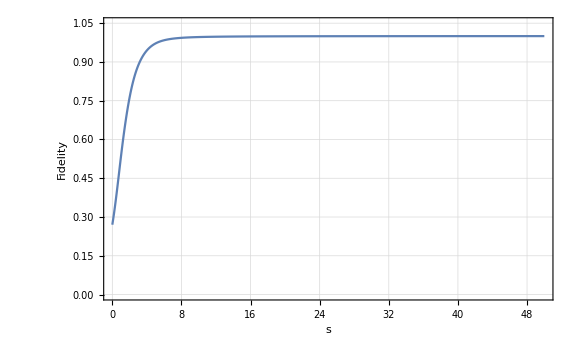

```mathematica
(*the fidelity*)
ListLinePlot[results⟦1⟧,PlotRange->{0,1.05},FrameLabel->{"s","Fidelity"},PlotTheme->"Detailed",BaseStyle->18,ImageSize->Large]
```

2-2

```mathematica
(*Initialization*)SeedRandom[0608];
ExampleQNNarchitecture2={2,2};TestInitialUnis2=InitialUnitaries@ExampleQNNarchitecture2;
```

```mathematica
(*start training for different learning rate*)
plotComparisons=QNNTraining[ExampleQNNarchitecture2,#,0.1,TestTrainingData,TestInitialUnis2,200]⟦1⟧&/@{2,1,0.5};//AbsoluteTiming
```

{4.49729,Null}

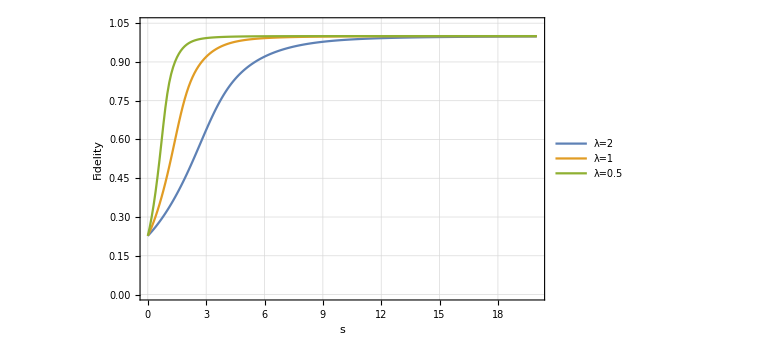

```mathematica
ListLinePlot[plotComparisons,PlotRange->{0,1.05},FrameLabel->{"s","Fidelity"},PlotTheme->"Detailed",PlotLegends->Placed[{"λ=2","λ=1","λ=0.5"},{0.85,0.4}],BaseStyle->18,ImageSize->Large]
```

## Tasks

Generalization  Bound

```mathematica
(*Formula for estimate of cost function*)
boundRand[n_,N_,D_]:=n/N+(N-n)/(N D (D+1)) (D+Min[n^2+1,D^2]);
(*Numerical estimation*)
AverageCost[n_,architecture_,ϵ_,λ_,dataSet_,intitialUnitaries_,steps_,rounds_]:=Module[{trainingSet,testSet,learnedUnitaries,outputStates,i},Monitor[Mean@Table[
trainingSet=RandomSample[dataSet,n];testSet=dataSet;
learnedUnitaries=QNNTraining[architecture,λ,ϵ,trainingSet,intitialUnitaries,steps]⟦2⟧;
outputStates=Feedforward[architecture,testSet,learnedUnitaries]⟦All,-1⟧;
CostFunction[testSet,outputStates],{i,rounds}],i]]
```

### D=4

```mathematica
(*Initialization*)SeedRandom[0608];Ν=10;𝔻=4;
QNNarchitecture={2,2};TestSet=TrainingData[Ν,RU@𝔻];
TestInitialUnis=InitialUnitaries@QNNarchitecture;
BoundPlotPointsD4=boundRand[#,Ν,𝔻]&/@N@Range[𝔻]
```

{0.37,0.56,0.79,1.}

```mathematica
PlotforGenTaskD4=Chop@Table[AverageCost[n,QNNarchitecture,0.1,1.5,TestSet,TestInitialUnis,100,20],{n,𝔻}];//AbsoluteTiming
```

{26.3519,Null}

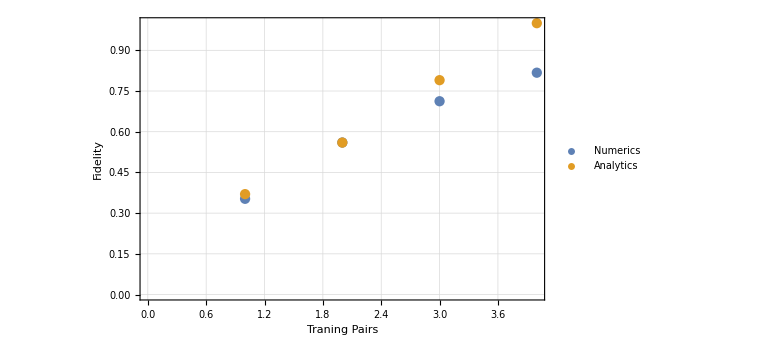

```mathematica
ListPlot[{PlotforGenTaskD4,BoundPlotPointsD4},FrameLabel->{"Traning Pairs","Fidelity"},PlotTheme->"Detailed",PlotLegends->Placed[{"Numerics","Analytics"},{0.87,0.2}],BaseStyle->18,ImageSize->Large]
```

### D=8

```mathematica
(*Initialization*)SeedRandom[0608];Ν=10;𝔻=8;
QNNarchitecture={3,3,3};TestSet=TrainingData[Ν,RU@𝔻];
TestInitialUnis=InitialUnitaries@QNNarchitecture;
BoundPlotPointsD8=boundRand[#,Ν,𝔻]&/@N@Range[𝔻]
```

{0.225,0.344444,0.475,0.608333,0.736111,0.85,0.941667,1.}

```mathematica
PlotforGenTaskD8=Chop@Table[AverageCost[n,QNNarchitecture,0.1,1.5,TestSet,TestInitialUnis,100,20],{n,𝔻}];//AbsoluteTiming
```

{1081.87,Null}

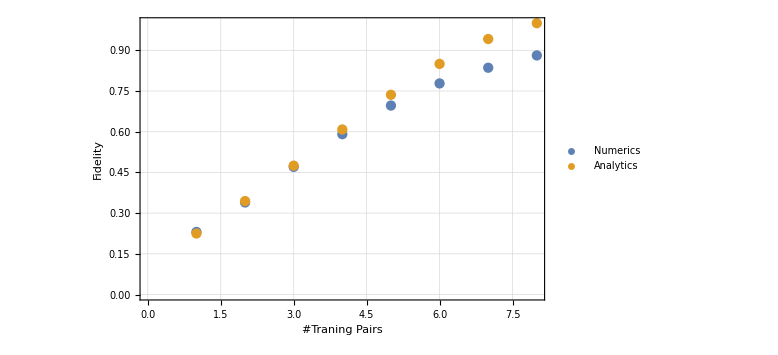

```mathematica
ListPlot[{PlotforGenTaskD8,BoundPlotPointsD8},FrameLabel->{"#Traning Pairs","Fidelity"},PlotTheme->"Detailed",PlotLegends->Placed[{"Numerics","Analytics"},{0.87,0.2}],BaseStyle->18,ImageSize->Large]
```

Robustness to Noisy Data

```mathematica
PlotData[dataSet_,noisySet_,architecture_,initialUnitaries_,steps_,ϵ_,λ_,N_,interval_]:=Module[{trainingSet,learnedUnitaries,outputStates,i},Monitor[Table[
trainingSet=Join[RandomSample [dataSet,N-i],RandomSample[noisySet,i]];
learnedUnitaries=QNNTraining[architecture,λ,ϵ,trainingSet,initialUnitaries,steps]⟦2⟧;
outputStates=Feedforward[architecture,dataSet,learnedUnitaries]⟦All,-1⟧;
{i,CostFunction[dataSet,outputStates]},{i,0,Ν,interval}],i]]
```

### 2-3-2

```mathematica
(*Initialization*)SeedRandom[0608];Ν=100;𝔻=4;
QNNarchitecture={2,3,2};
TestDataSet=TrainingData[Ν,RU@𝔻];
TestNoisySet=Table[{RandomState@𝔻,RandomState@𝔻},Ν];
TestInitialUnis=InitialUnitaries@QNNarchitecture;
```

```mathematica
noisyResults=PlotData[TestDataSet,TestNoisySet,QNNarchitecture,TestInitialUnis,100,0.1,1,Ν,5];//AbsoluteTiming
```

{1013.81,Null}

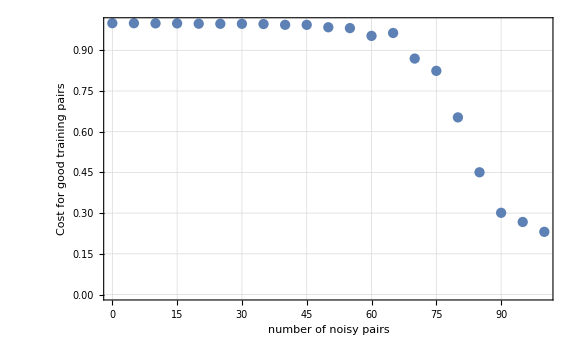

```mathematica
ListPlot[noisyResults,FrameLabel->{"number of noisy pairs","Cost for good training pairs"},PlotTheme->"Detailed",BaseStyle->18,ImageSize->Large]
```

### 2-2

```mathematica
(*Initialization*)SeedRandom[0608];Ν=100;𝔻=4;
QNNarchitecture={2,2};
TestDataSet=TrainingData[Ν,RU@𝔻];
TestNoisySet=Table[{RandomState@𝔻,RandomState@𝔻},Ν];
TestInitialUnis=InitialUnitaries@QNNarchitecture;
```

```mathematica
noisyResults=PlotData[TestDataSet,TestNoisySet,QNNarchitecture,TestInitialUnis,100,0.1,1,Ν,5];//AbsoluteTiming
```

{147.616,Null}

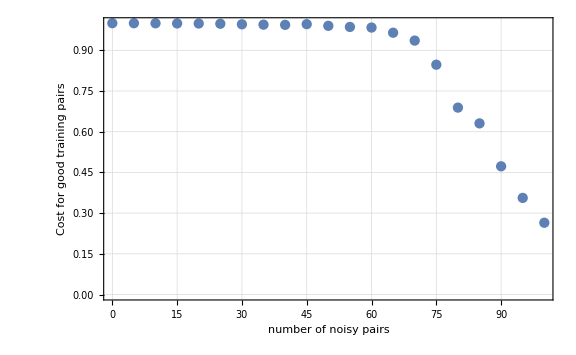

```mathematica
ListPlot[noisyResults,FrameLabel->{"number of noisy pairs","Cost for good training pairs"},PlotTheme->"Detailed",BaseStyle->18,ImageSize->Large]
```

Big Networks

### 2-3-3-2

```mathematica
(*Initialization*)SeedRandom[0608];Ν=5;𝔻=4;
ExampleQNNarchitecture={2,3,3,2};TestTrainingData=TrainingData[Ν,RU@𝔻];
TestInitialUnis=InitialUnitaries@ExampleQNNarchitecture;
```

```mathematica
(*start training*)
results=QNNTraining[ExampleQNNarchitecture,3,0.1,TestTrainingData,TestInitialUnis,500];//AbsoluteTiming
```

{33.0893,Null}

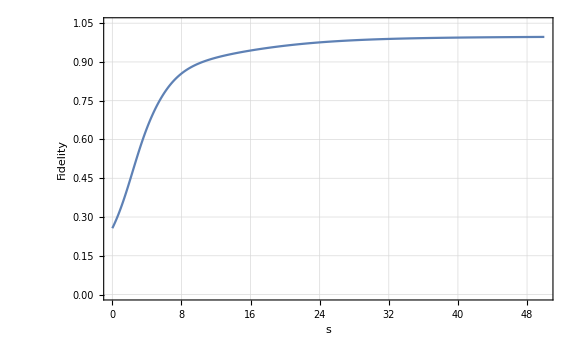

```mathematica
(*the fidelity*)
ListLinePlot[results⟦1⟧,PlotRange->{0,1.05},FrameLabel->{"s","Fidelity"},PlotTheme->"Detailed",BaseStyle->18,ImageSize->Large]
```

### 2-3-4-3-2

```mathematica
(*Initialization*)SeedRandom[0608];Ν=5;𝔻=4;
ExampleQNNarchitecture={2,3,4,3,2};TestTrainingData=TrainingData[Ν,RU@𝔻];
TestInitialUnis=InitialUnitaries@ExampleQNNarchitecture;
```

```mathematica
(*start training*)
results=QNNTraining[ExampleQNNarchitecture,4,0.1,TestTrainingData,TestInitialUnis,500];//AbsoluteTiming
```

{173.759,Null}

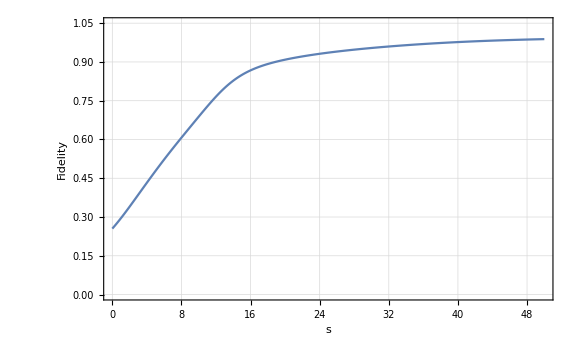

```mathematica
(*the fidelity*)
ListLinePlot[results⟦1⟧,PlotRange->{0,1.05},FrameLabel->{"s","Fidelity"},PlotTheme->"Detailed",BaseStyle->18,ImageSize->Large]
```